```mathematica
q[p_,k_]:=1-(1-p)^k
expNmut[L_,k_,p_]:=L*q[p,k]
```

```mathematica
expNmut[a,b,c]
```

a (1-(1-c)^b)

```mathematica
varNmut[L_,k_,p_]:=L*(1-q[p,k])*(q[p,k]*(2*k+(2/p)-1)-2*k)+k*(k-1)*(1-q[p,k])^2+(2*(1-q[p,k])/(p^2))*((1+(k-1)*(1-q[p,k]))*p-q[p,k])
```

```mathematica
varNmut[L,k,p]
```

L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k+(-1+k) k (1-p)^(2 k)+(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2

```mathematica
expNmutSquared[L_,k_,p_]:=varNmut[L,k,p]+expNmut[L,k,p]^2
```

```mathematica
expNmutSquared[L,k,p]
```

L^2 (1-(1-p)^k)^2+L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k+(-1+k) k (1-p)^(2 k)+(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2

```mathematica
biasFactor[L_,s_]:=1-(1-s)^L
```

```mathematica
biasFactor[L,s]
```

1-(1-s)^L

```mathematica
term1[L_,s_]:=(1-s)/(s*L^3*biasFactor[L,s]^2)
```

```mathematica
term1[L,s]
```

(1-s)/(L^3 (1-(1-s)^L)^2 s)

```mathematica
term2[L_,k_,p_]:=L*expNmut[L,k,p]-expNmutSquared[L,k,p]
```

```mathematica
term2[L,k,p]
```

L^2 (1-(1-p)^k)-L^2 (1-(1-p)^k)^2-L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k-(-1+k) k (1-p)^(2 k)-(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2

```mathematica
term3[L_,k_,p_]:=varNmut[L,k,p]/L^2
```

```mathematica
term3[L,k,p]
```

(L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k+(-1+k) k (1-p)^(2 k)+(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2)/L^2

```mathematica
varCScale[L_,k_,p_,s_]:=term1[L,s]*term2[L,k,p]+term3[L,k,p]
```

```mathematica
varCScale[L,k,p,s]
```

(L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k+(-1+k) k (1-p)^(2 k)+(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2)/L^2+((L^2 (1-(1-p)^k)-L^2 (1-(1-p)^k)^2-L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k-(-1+k) k (1-p)^(2 k)-(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2) (1-s))/(L^3 (1-(1-s)^L)^2 s)

```mathematica
f[L_,k_,p_,s_,zAlpha_]:=(1-p)^k-zAlpha*Sqrt[varCScale[L,k,p,s]]
```

```mathematica
f[L,k,p,s,z]
```

(1-p)^k-√((L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k+(-1+k) k (1-p)^(2 k)+(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2)/L^2+((L^2 (1-(1-p)^k)-L^2 (1-(1-p)^k)^2-L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k-(-1+k) k (1-p)^(2 k)-(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2) (1-s))/(L^3 (1-(1-s)^L)^2 s)) z

```mathematica
D[f[L,k,p,s,z],p]
```

-k (1-p)^(-1+k)-((1/L^2(-k L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^(-1+k)+L (k (-1+2 k+2/p) (1-p)^(-1+k)-(2 (1-(1-p)^k))/p^2) (1-p)^k-2 (-1+k) k^2 (1-p)^(-1+2 k)-(4 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^3-(2 k (1-p)^(-1+k) (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2+(2 (1-p)^k (1-k (1-p)^(-1+k)+(-1+k) (1-p)^k-(-1+k) k (1-p)^(-1+k) p))/p^2)+1/(L^3 (1-(1-s)^L)^2 s)(k L^2 (1-p)^(-1+k)+k L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^(-1+k)-2 k L^2 (1-(1-p)^k) (1-p)^(-1+k)-L (k (-1+2 k+2/p) (1-p)^(-1+k)-(2 (1-(1-p)^k))/p^2) (1-p)^k+2 (-1+k) k^2 (1-p)^(-1+2 k)+(4 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^3+(2 k (1-p)^(-1+k) (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2-(2 (1-p)^k (1-k (1-p)^(-1+k)+(-1+k) (1-p)^k-(-1+k) k (1-p)^(-1+k) p))/p^2) (1-s)) z)/(2 √((L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k+(-1+k) k (1-p)^(2 k)+(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2)/L^2+((L^2 (1-(1-p)^k)-L^2 (1-(1-p)^k)^2-L (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k-(-1+k) k (1-p)^(2 k)-(2 (1-p)^k (-1+(1-p)^k+(1+(-1+k) (1-p)^k) p))/p^2) (1-s))/(L^3 (1-(1-s)^L)^2 s)))

```mathematica
Series[%,L->Infinity]
```

-k (1-p)^(-1+k)+(((k (-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^(-1+k)-(k (-1+2 k+2/p) (1-p)^(-1+k)-(2 (1-(1-p)^k))/p^2) (1-p)^k) z)/(2 L)+O[1/L]^2)/(√((((-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k)/L+O[1/L]^2)+(((-1+(1-p)^k) (1-p)^k (-1+s))/(s L)+O[1/L]^2)/((1-ⅇ^(Log[1-s] L+O[1/L]^4))^2)))+(-(k (-1+2 (1-p)^k) (1-p)^k (-1+s) z)/(2 ((-1+p) s) L)+O[1/L]^2)/((1-ⅇ^(Log[1-s] L+O[1/L]^4))^2 √((((-2 k+(1-(1-p)^k) (-1+2 k+2/p)) (1-p)^k)/L+O[1/L]^2)+(((-1+(1-p)^k) (1-p)^k (-1+s))/(s L)+O[1/L]^2)/((1-ⅇ^(Log[1-s] L+O[1/L]^4))^2)))

```mathematica
fJaccard[L_,N_,zAlpha_,s_]:=(L-N)/(L+N)+zAlpha*Sqrt[2*N*(L-N)*(1-s)/(s*(L+N)^3*( 1-(1-s)^(L+N) ))]
```

```mathematica
fJaccard[L,N,z,s]
```

(L-N)/(L+N)+√2 √(((L-N) N (1-s))/((L+N)^3 (1-(1-s)^(L+N)) s)) z

```mathematica
D[fJaccard[L,N,z,s], N]
```

-(L-N)/(L+N)^2-1/(L+N)+(z (-(3 (L-N) N (1-s))/((L+N)^4 (1-(1-s)^(L+N)) s)+((L-N) (1-s))/((L+N)^3 (1-(1-s)^(L+N)) s)-(N (1-s))/((L+N)^3 (1-(1-s)^(L+N)) s)+((L-N) N (1-s)^(1+L+N) Log[1-s])/((L+N)^3 (1-(1-s)^(L+N))^2 s)))/(√2 √(((L-N) N (1-s))/((L+N)^3 (1-(1-s)^(L+N)) s)))

```mathematica
Series[D[fJaccard[L,N,z,s], N],L-> Infinity]
```

(-2/L+O[1/L]^2)+√((-(N (-1+s))/(s L^2)+O[1/L]^3)/(1-ⅇ^(Log[1-s] L+O[1/L]^0))) (-(3 z)/(√2 L)+O[1/L]^2)+(√((-(N (-1+s))/(s L^2)+O[1/L]^3)/(1-ⅇ^(Log[1-s] L+O[1/L]^0))) (-z/(√2 L)+O[1/L]^2))/(1-ⅇ^(Log[1-s] L+O[1/L]^0))+(ⅇ^(Log[1-s] L+O[1/L]^0) √((-(N (-1+s))/(s L^2)+O[1/L]^3)/(1-ⅇ^(Log[1-s] L+O[1/L]^0))) (z/(√2 L)+O[1/L]^2))/(1-ⅇ^(Log[1-s] L+O[1/L]^0))+√((-(N (-1+s))/(s L^2)+O[1/L]^3)/(1-ⅇ^(Log[1-s] L+O[1/L]^0))) (z/(√2 N)+O[1/L]^2)+(ⅇ^(Log[1-s] L+O[1/L]^0) √((-(N (-1+s))/(s L^2)+O[1/L]^3)/(1-ⅇ^(Log[1-s] L+O[1/L]^0))) (-(z Log[1-s])/(√2 (-1+s))+O[1/L]^2))/(1-ⅇ^(Log[1-s] L+O[1/L]^0))

```mathematica
LL = 100000
KK = 21
mutRate = 0.05
scaleFactor = 0.1
conf = 0.95
```

100000

21

0.05

0.1

0.95

```mathematica
EE = expNmut[LL, KK, mutRate]
```

65943.8

```mathematica
VV = varNmut[LL, KK, mutRate]
```

388710.

```mathematica
PDF[NormalDistribution[EE, Sqrt[VV]]]
```

Function[x,0.000639878 ⅇ^(-1.28631×10^-6 (-65943.8+x)^2)]

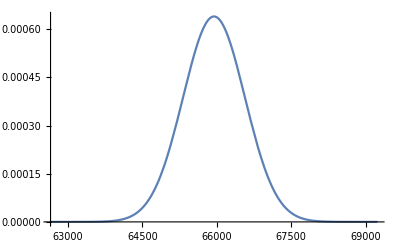

```mathematica
Plot[ 0.000639878203400662 ⅇ^(-1.2863066243278652*^-6 (-65943.83737118849+y)^2), {y,EE(0.95),EE(1.05)}]
```

```mathematica
TransformedDistribution[(LL-X)/(LL+X),X\[Distributed]NormalDistribution[EE,Sqrt[VV]]]
```

TransformedDistribution[(100000-x)/(100000+x),x\[Distributed]NormalDistribution[65943.8,623.466]]

```mathematica
PDF[TransformedDistribution[(100000-x)/(100000+x),x\[Distributed]NormalDistribution[65943.83737118849,623.4659631805487]]]
```

Function[x,Piecewise[{{(127.976 ⅇ^(-(35421.5 (0.205227-1. x)^2)/(1.+x)^2))/(1.+x)^2, x≠-1}, {Indeterminate, True}}],Listable]

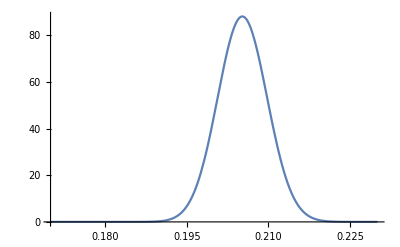

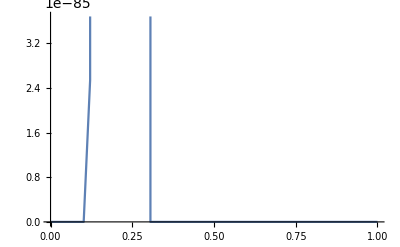

```mathematica
Plot[(127.97564068013236 ⅇ^(-(35421.48493328825 (0.20522704047534823-1. x)^2)/(1.+x)^2))/(1.+x)^2,{x,0.17, 0.23}]
```